## Relation to results derived under a discrete space model without gene-flow

In matrix form the non-spatial model can be written dz=(b+M.z)dt+σ dW where

```mathematica
M={{-Subscript[G, H] Subscript[A, H]+Subscript[G, H] Subscript[B, H],-Subscript[G, H] Subscript[B, H]},{Subscript[G, P] Subscript[B, P],-Subscript[G, P] Subscript[A, P]-Subscript[G, P] Subscript[B, P]}};
b={{Subscript[G, H] Subscript[A, H] Subscript[ζ, H]},{Subscript[G, P] Subscript[A, P] Subscript[ζ, P]}};
σ={{√(Subscript[G, H]/Subscript[n, H]),0},{0,√(Subscript[G, P]/Subscript[n, P])}};
M//MatrixForm
b//MatrixForm
σ//MatrixForm
```

(-A_H G_H+B_H G_H | -B_H G_H
B_P G_P | -A_P G_P-B_P G_P)

(A_H G_H ζ_H
A_P G_P ζ_P)

(√(G_H/n_H) | 0
0 | √(G_P/n_P))

This is an OU which is traditionally written in the form dz=θ.(μ-z)dt+σ dW
Relating the two, we get

```mathematica
μ=FullSimplify[-Inverse[M].b];
θ=-M;
μ//MatrixForm
θ//MatrixForm
```

((A_H (A_P+B_P) ζ_H-A_P B_H ζ_P)/(-A_P B_H+A_H (A_P+B_P))
(-A_H B_P ζ_H+A_P (-A_H+B_H) ζ_P)/(A_P B_H-A_H (A_P+B_P)))

(A_H G_H-B_H G_H | B_H G_H
-B_P G_P | A_P G_P+B_P G_P)

```mathematica
Σt=Integrate[MatrixExp[θ(s-t)].σ.Transpose[σ].MatrixExp[Transpose[θ](s-t)],{s,0,t},Assumptions->{Subscript[A, H]>0,Subscript[A, P]>0,Subscript[B, H]>0,Subscript[A, H]>Subscript[B, H],Subscript[B, P]>0,Subscript[G, H]>0,Subscript[G, P]>0,Subscript[n, H]>0,Subscript[n, P]>0}];
```

```mathematica
Σ=Limit[Σt,{t->∞},Assumptions->{Subscript[A, H]>0,Subscript[A, P]>0,Subscript[B, H]>0,Subscript[A, H]>Subscript[B, H],Subscript[B, P]>0,Subscript[G, H]>0,Subscript[G, P]>0,Subscript[n, H]>0,Subscript[n, P]>0}];
```

$Aborted

```mathematica
{{ConditionalExpression[(2 Subscript[G, H] Subscript[G, P] (Subscript[B, H]^2 Subscript[G, H] Subscript[n, H]-Subscript[A, P] Subscript[B, H] Subscript[G, H] Subscript[n, P]+(Subscript[A, P]+Subscript[B, P]) (Subscript[A, H] Subscript[G, H]+(Subscript[A, P]+Subscript[B, P]) Subscript[G, P]) Subscript[n, P]))/((Subscript[A, H] Subscript[G, H]-Subscript[B, H] Subscript[G, H]+(Subscript[A, P]+Subscript[B, P]) Subscript[G, P]) (Subscript[A, H] Subscript[G, H]-Subscript[B, H] Subscript[G, H]+Subscript[A, P] Subscript[G, P]+Subscript[B, P] Subscript[G, P]-√(-4 (-Subscript[A, P] Subscript[B, H]+Subscript[A, H] (Subscript[A, P]+Subscript[B, P])) Subscript[G, H] Subscript[G, P]+(Subscript[A, H] Subscript[G, H]-Subscript[B, H] Subscript[G, H]+(Subscript[A, P]+Subscript[B, P]) Subscript[G, P])^2)) (Subscript[A, H] Subscript[G, H]-Subscript[B, H] Subscript[G, H]+Subscript[A, P] Subscript[G, P]+Subscript[B, P] Subscript[G, P]+√(-4 (-Subscript[A, P] Subscript[B, H]+Subscript[A, H] (Subscript[A, P]+Subscript[B, P])) Subscript[G, H] Subscript[G, P]+(Subscript[A, H] Subscript[G, H]-Subscript[B, H] Subscript[G, H]+(Subscript[A, P]+Subscript[B, P]) Subscript[G, P])^2)) Subscript[n, H] Subscript[n, P]), √(-4 (-Subscript[A, P] Subscript[B, H]+Subscript[A, H] (Subscript[A, P]+Subscript[B, P])) Subscript[G, H] Subscript[G, P]+(Subscript[A, H] Subscript[G, H]-Subscript[B, H] Subscript[G, H]+(Subscript[A, P]+Subscript[B, P]) Subscript[G, P])^2)∈Reals&&Subscript[A, H] Subscript[G, H]+Subscript[A, P] Subscript[G, P]+Subscript[B, P] Subscript[G, P]>Subscript[B, H] Subscript[G, H]&&√(-4 (-Subscript[A, P] Subscript[B, H]+Subscript[A, H] (Subscript[A, P]+Subscript[B, P])) Subscript[G, H] Subscript[G, P]+(Subscript[A, H] Subscript[G, H]-Subscript[B, H] Subscript[G, H]+(Subscript[A, P]+Subscript[B, P]) Subscript[G, P])^2)>0&&Subscript[B, H] Subscript[G, H]+√(-4 (-Subscript[A, P] Subscript[B, H]+Subscript[A, H] (Subscript[A, P]+Subscript[B, P])) Subscript[G, H] Subscript[G, P]+(Subscript[A, H] Subscript[G, H]-Subscript[B, H] Subscript[G, H]+(Subscript[A, P]+Subscript[B, P]) Subscript[G, P])^2)<Subscript[A, H] Subscript[G, H]+Subscript[A, P] Subscript[G, P]+Subscript[B, P] Subscript[G, P]&&Subscript[A, H] Subscript[G, H]+Subscript[A, P] Subscript[G, P]+Subscript[B, P] Subscript[G, P]+√(-4 (-Subscript[A, P] Subscript[B, H]+Subscript[A, H] (Subscript[A, P]+Subscript[B, P])) Subscript[G, H] Subscript[G, P]+(Subscript[A, H] Subscript[G, H]-Subscript[B, H] Subscript[G, H]+(Subscript[A, P]+Subscript[B, P]) Subscript[G, P])^2)>Subscript[B, H] Subscript[G, H]],ConditionalExpression[-(2 Subscript[G, H] Subscript[G, P] (Subscript[A, H] Subscript[B, H] Subscript[G, H] Subscript[n, H]-Subscript[B, H]^2 Subscript[G, H] Subscript[n, H]-Subscript[B, P] (Subscript[A, P]+Subscript[B, P]) Subscript[G, P] Subscript[n, P]))/((Subscript[A, H] Subscript[G, H]-Subscript[B, H] Subscript[G, H]+(Subscript[A, P]+Subscript[B, P]) Subscript[G, P]) (Subscript[A, H] Subscript[G, H]-Subscript[B, H] Subscript[G, H]+Subscript[A, P] Subscript[G, P]+Subscript[B, P] Subscript[G, P]-√(-4 (-Subscript[A, P] Subscript[B, H]+Subscript[A, H] (Subscript[A, P]+Subscript[B, P])) Subscript[G, H] Subscript[G, P]+(Subscript[A, H] Subscript[G, H]-Subscript[B, H] Subscript[G, H]+(Subscript[A, P]+Subscript[B, P]) Subscript[G, P])^2)) (Subscript[A, H] Subscript[G, H]-Subscript[B, H] Subscript[G, H]+Subscript[A, P] Subscript[G, P]+Subscript[B, P] Subscript[G, P]+√(-4 (-Subscript[A, P] Subscript[B, H]+Subscript[A, H] (Subscript[A, P]+Subscript[B, P])) Subscript[G, H] Subscript[G, P]+(Subscript[A, H] Subscript[G, H]-Subscript[B, H] Subscript[G, H]+(Subscript[A, P]+Subscript[B, P]) Subscript[G, P])^2)) Subscript[n, H] Subscript[n, P]), ]},{ConditionalExpression[-(2 Subscript[G, H] Subscript[G, P] (Subscript[A, H] Subscript[B, H] Subscript[G, H] Subscript[n, H]-Subscript[B, H]^2 Subscript[G, H] Subscript[n, H]-Subscript[B, P] (Subscript[A, P]+Subscript[B, P]) Subscript[G, P] Subscript[n, P]))/((Subscript[A, H] Subscript[G, H]-Subscript[B, H] Subscript[G, H]+(Subscript[A, P]+Subscript[B, P]) Subscript[G, P]) (Subscript[A, H] Subscript[G, H]-Subscript[B, H] Subscript[G, H]+Subscript[A, P] Subscript[G, P]+Subscript[B, P] Subscript[G, P]-√(-4 (-Subscript[A, P] Subscript[B, H]+Subscript[A, H] (Subscript[A, P]+Subscript[B, P])) Subscript[G, H] Subscript[G, P]+(Subscript[A, H] Subscript[G, H]-Subscript[B, H] Subscript[G, H]+(Subscript[A, P]+Subscript[B, P]) Subscript[G, P])^2)) (Subscript[A, H] Subscript[G, H]-Subscript[B, H] Subscript[G, H]+Subscript[A, P] Subscript[G, P]+Subscript[B, P] Subscript[G, P]+√(-4 (-Subscript[A, P] Subscript[B, H]+Subscript[A, H] (Subscript[A, P]+Subscript[B, P])) Subscript[G, H] Subscript[G, P]+(Subscript[A, H] Subscript[G, H]-Subscript[B, H] Subscript[G, H]+(Subscript[A, P]+Subscript[B, P]) Subscript[G, P])^2)) Subscript[n, H] Subscript[n, P]), ],ConditionalExpression[(2 Subscript[G, H] Subscript[G, P] (Subscript[A, H]^2 Subscript[G, H] Subscript[n, H]+Subscript[B, H]^2 Subscript[G, H] Subscript[n, H]-Subscript[A, P] Subscript[B, H] Subscript[G, P] Subscript[n, H]+Subscript[A, H] (-2 Subscript[B, H] Subscript[G, H]+(Subscript[A, P]+Subscript[B, P]) Subscript[G, P]) Subscript[n, H]+Subscript[B, P]^2 Subscript[G, P] Subscript[n, P]))/((Subscript[A, H] Subscript[G, H]-Subscript[B, H] Subscript[G, H]+(Subscript[A, P]+Subscript[B, P]) Subscript[G, P]) (Subscript[A, H] Subscript[G, H]-Subscript[B, H] Subscript[G, H]+Subscript[A, P] Subscript[G, P]+Subscript[B, P] Subscript[G, P]-√(-4 (-Subscript[A, P] Subscript[B, H]+Subscript[A, H] (Subscript[A, P]+Subscript[B, P])) Subscript[G, H] Subscript[G, P]+(Subscript[A, H] Subscript[G, H]-Subscript[B, H] Subscript[G, H]+(Subscript[A, P]+Subscript[B, P]) Subscript[G, P])^2)) (Subscript[A, H] Subscript[G, H]-Subscript[B, H] Subscript[G, H]+Subscript[A, P] Subscript[G, P]+Subscript[B, P] Subscript[G, P]+√(-4 (-Subscript[A, P] Subscript[B, H]+Subscript[A, H] (Subscript[A, P]+Subscript[B, P])) Subscript[G, H] Subscript[G, P]+(Subscript[A, H] Subscript[G, H]-Subscript[B, H] Subscript[G, H]+(Subscript[A, P]+Subscript[B, P]) Subscript[G, P])^2)) Subscript[n, H] Subscript[n, P]), ]}}
```

Expressions for variance and covariance of mean traits at statistical equilibrium

```mathematica
Subscript[v, H]=FullSimplify[Σ[[1,1]]][[1]]
```

(B_H^2 G_H n_H+((-A_P B_H+A_H (A_P+B_P)) G_H+(A_P+B_P)^2 G_P) n_P)/(2 (-A_P B_H+A_H (A_P+B_P)) ((A_H-B_H) G_H+(A_P+B_P) G_P) n_H n_P)

```mathematica
Subscript[v, P]=FullSimplify[Σ[[2,2]]][[1]]
```

(((A_H-B_H)^2 G_H+(-A_P B_H+A_H (A_P+B_P)) G_P) n_H+B_P^2 G_P n_P)/(2 (-A_P B_H+A_H (A_P+B_P)) ((A_H-B_H) G_H+(A_P+B_P) G_P) n_H n_P)

```mathematica
Subscript[c, HP]=FullSimplify[Σ[[1,2]]][[1]]
```

(B_H (-A_H+B_H) G_H n_H+B_P (A_P+B_P) G_P n_P)/(2 (-A_P B_H+A_H (A_P+B_P)) ((A_H-B_H) G_H+(A_P+B_P) G_P) n_H n_P)

```mathematica
FullSimplify[ExpandAll[(1/(2 Subscript[n, P])+Subscript[B, P] Subscript[c, HP])/(Subscript[A, P]+Subscript[B, P])]]==Subscript[v, P]
```

True

```mathematica
FullSimplify[ExpandAll[(1/(2 Subscript[n, H])-Subscript[B, H] Subscript[c, HP])/(Subscript[A, H]-Subscript[B, H])]]==Subscript[v, H]
```

True

```mathematica
FullSimplify[Subscript[v, H]/.{Subscript[B, H]^2->0}]
```

## Relation to results derived under an island model

```mathematica
Subscript[dz, H,k]=Subscript[G, H](Subscript[A, H](Subscript[θ, H]-Subscript[z, H,k])-Subscript[B, H](Subscript[z, P,k]-Subscript[z, H,k]))+Subscript[d, H](Subscript[μ, H]-Subscript[z, H,k])+√(Subscript[G, H]/Subscript[n, H])Subscript[dW, H,k]
Subscript[dz, P,k]=Subscript[G, P](Subscript[A, P](Subscript[θ, P]-Subscript[z, P,k])+Subscript[B, P](Subscript[z, H,k]-Subscript[z, P,k]))+Subscript[d, P](Subscript[μ, P]-Subscript[z, P,k])+√(Subscript[G, P]/Subscript[n, P])Subscript[dW, P,k]
Subscript[dμ, H]=Subscript[G, H](Subscript[A, H](Subscript[θ, H]-Subscript[μ, H])-Subscript[B, H](Subscript[μ, P]-Subscript[μ, H]))+√(Subscript[G, H]/Subscript[n, H])Subscript[OverHat[dW], H]
Subscript[dμ, P]=Subscript[G, P](Subscript[A, P](Subscript[θ, P]-Subscript[μ, P])+Subscript[B, P](Subscript[μ, H]-Subscript[μ, P]))+√(Subscript[G, P]/Subscript[n, P])Subscript[OverHat[dW], P]
```

√(G_H/n_H) dW_(H,k)+d_H (μ_H-z_(H,k))+G_H (A_H (θ_H-z_(H,k))-B_H (-z_(H,k)+z_(P,k)))

√(G_P/n_P) dW_(P,k)+G_P (A_P (θ_P-z_(P,k))+B_P (z_(H,k)-z_(P,k)))+d_P (μ_P-z_(P,k))

G_H (A_H (θ_H-μ_H)-B_H (-μ_H+μ_P))+√(G_H/n_H) OverHat[dW]_H

G_P (A_P (θ_P-μ_P)+B_P (μ_H-μ_P))+√(G_P/n_P) OverHat[dW]_P

```mathematica
Subscript[dV, H]=FullSimplify[Collect[Expand[(2 Subscript[z, H,k] Subscript[dz, H,k]+Subscript[G, H]/Subscript[n, H])-2 Subscript[μ, H] Subscript[dμ, H]],{Subscript[G, H],Subscript[G, P],Subscript[d, H],Subscript[d, P],√(Subscript[G, H]/Subscript[n, H]),√(Subscript[G, P]/Subscript[n, P])}]/.{Subscript[z, P,k]^2->Subscript[V, P]+Subscript[μ, P]^2,Subscript[z, H,k]^2->Subscript[V, H]+Subscript[μ, H]^2,Subscript[z, H,k] Subscript[z, P,k]->Subscript[c, HP]+Subscript[μ, H] Subscript[μ, P],Subscript[z, H,k]->Subscript[μ, H],Subscript[z, P,k]->Subscript[μ, P],Subscript[dW, H,k]->Subscript[OverHat[dW], H],Subscript[dW, P,k]->Subscript[OverHat[dW], P]}]
```

-2 d_H V_H+G_H (1/n_H-2 A_H V_H+2 B_H (-c_HP+V_H))

```mathematica
Solve[Subscript[dV, H]==0,Subscript[V, H]]
```

{{V_H→(G_H-2 B_H c_HP G_H n_H)/(2 (d_H+A_H G_H-B_H G_H) n_H)}}

```mathematica
Subscript[dV, P]=FullSimplify[Collect[Expand[(2 Subscript[z, P,k] Subscript[dz, P,k]+Subscript[G, P]/Subscript[n, P])-2 Subscript[μ, P] Subscript[dμ, P]],{Subscript[G, H],Subscript[G, P],Subscript[d, H],Subscript[d, P],√(Subscript[G, H]/Subscript[n, H]),√(Subscript[G, P]/Subscript[n, P])}]/.{Subscript[z, P,k]^2->Subscript[V, P]+Subscript[μ, P]^2,Subscript[z, H,k]^2->Subscript[V, H]+Subscript[μ, H]^2,Subscript[z, H,k] Subscript[z, P,k]->Subscript[c, HP]+Subscript[μ, H] Subscript[μ, P],Subscript[z, H,k]->Subscript[μ, H],Subscript[z, P,k]->Subscript[μ, P],Subscript[dW, H,k]->Subscript[OverHat[dW], H],Subscript[dW, P,k]->Subscript[OverHat[dW], P]}]
```

-2 d_P V_P+G_P (2 B_P c_HP+1/n_P-2 (A_P+B_P) V_P)

```mathematica
Solve[Subscript[dV, P]==0,Subscript[V, P]]
```

{{V_P→(G_P+2 B_P c_HP G_P n_P)/(2 (d_P+A_P G_P+B_P G_P) n_P)}}

```mathematica
Subscript[dC, HP]=FullSimplify[Collect[Expand[(Subscript[z, H,k] Subscript[dz, P,k]+Subscript[z, P,k] Subscript[dz, H,k])-Subscript[μ, H] Subscript[dμ, P]-Subscript[μ, P] Subscript[dμ, H]],{Subscript[G, H],Subscript[G, P],Subscript[d, H],Subscript[d, P],√(Subscript[G, H]/Subscript[n, H]),√(Subscript[G, P]/Subscript[n, P])}]/.{Subscript[z, P,k]^2->Subscript[V, P]+Subscript[μ, P]^2,Subscript[z, H,k]^2->Subscript[V, H]+Subscript[μ, H]^2,Subscript[z, H,k] Subscript[z, P,k]->Subscript[c, HP]+Subscript[μ, H] Subscript[μ, P],Subscript[z, H,k]->Subscript[μ, H],Subscript[z, P,k]->Subscript[μ, P],Subscript[dW, H,k]->Subscript[OverHat[dW], H],Subscript[dW, P,k]->Subscript[OverHat[dW], P]}]
```

-c_HP (d_H+d_P+(A_H-B_H) G_H+(A_P+B_P) G_P)+B_P G_P V_H-B_H G_H V_P

```mathematica
Solve[Subscript[dC, HP]==0,Subscript[c, HP]]
```

{{c_HP→(B_P G_P V_H-B_H G_H V_P)/(d_H+d_P+A_H G_H-B_H G_H+A_P G_P+B_P G_P)}}

```mathematica
slns=FullSimplify[Solve[{Subscript[dV, H]==0,Subscript[dV, P]==0,Subscript[dC, HP]==0},{Subscript[V, H],Subscript[V, P],Subscript[c, HP]}]]
```

{{V_H→(G_H (B_H^2 G_H G_P n_H-B_H G_H (d_P+A_P G_P) n_P+(d_P+(A_P+B_P) G_P) (d_H+d_P+A_H G_H+(A_P+B_P) G_P) n_P))/(2 (d_H+d_P+(A_H-B_H) G_H+(A_P+B_P) G_P) (d_H (d_P+(A_P+B_P) G_P)+G_H (-B_H (d_P+A_P G_P)+A_H (d_P+(A_P+B_P) G_P))) n_H n_P),V_P→-((2 G_P ((B_P^2 G_H G_P)/n_H+(B_H B_P G_H G_P)/n_P+((d_H+(A_H-B_H) G_H) (d_H+d_P+(A_H-B_H) G_H+(A_P+B_P) G_P))/n_P))/(4 B_H B_P G_H (-d_H+(-A_H+B_H) G_H) G_P-(-2 d_P-2 (A_P+B_P) G_P) (-2 B_H B_P G_H G_P-2 (d_H+(A_H-B_H) G_H) (d_H+d_P+(A_H-B_H) G_H+(A_P+B_P) G_P)))),c_HP→(G_H G_P (B_H (-d_H+(-A_H+B_H) G_H) n_H+B_P (d_P+(A_P+B_P) G_P) n_P))/(2 (d_H+d_P+(A_H-B_H) G_H+(A_P+B_P) G_P) (d_H (d_P+(A_P+B_P) G_P)+G_H (-B_H (d_P+A_P G_P)+A_H (d_P+(A_P+B_P) G_P))) n_H n_P)}}

```mathematica
Subscript[COV, HP]=Subscript[c, HP]/.slns[[1]]
```

(G_H G_P (B_H (-d_H+(-A_H+B_H) G_H) n_H+B_P (d_P+(A_P+B_P) G_P) n_P))/(2 (d_H+d_P+(A_H-B_H) G_H+(A_P+B_P) G_P) (d_H (d_P+(A_P+B_P) G_P)+G_H (-B_H (d_P+A_P G_P)+A_H (d_P+(A_P+B_P) G_P))) n_H n_P)

```mathematica
subs={Subscript[G, H]->10,Subscript[G, P]->10,Subscript[A, H]->0.01,Subscript[A, P]->0.01,Subscript[B, H]->0.005,Subscript[B, P]->0.005,Subscript[n, H]->1000,Subscript[n, P]->1000,Subscript[d, H]->dr,Subscript[d, P]->1/dr};
subs2={Subscript[G, H]->10,Subscript[G, P]->10,Subscript[A, H]->0.01,Subscript[A, P]->0.01,Subscript[B, H]->0.005,Subscript[B, P]->0.005,Subscript[n, H]->1000,Subscript[n, P]->1000,Subscript[d, H]->10*dr,Subscript[d, P]->10/dr};
subs3={Subscript[G, H]->10,Subscript[G, P]->10,Subscript[A, H]->0.01,Subscript[A, P]->0.01,Subscript[B, H]->0.005,Subscript[B, P]->0.005,Subscript[n, H]->1000,Subscript[n, P]->1000,Subscript[d, H]->1000*dr,Subscript[d, P]->1000/dr};
subs4={Subscript[G, H]->10,Subscript[G, P]->10,Subscript[A, H]->0.01,Subscript[A, P]->0.01,Subscript[B, H]->0.005,Subscript[B, P]->0.005,Subscript[n, H]->1000,Subscript[n, P]->1000,Subscript[d, H]->M*dr,Subscript[d, P]->M/dr};
```

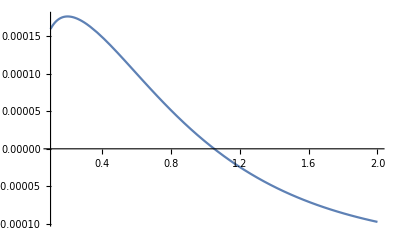

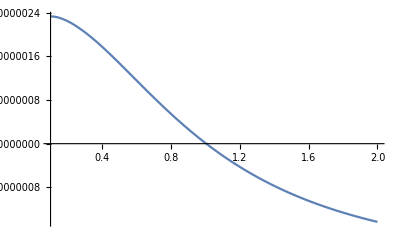

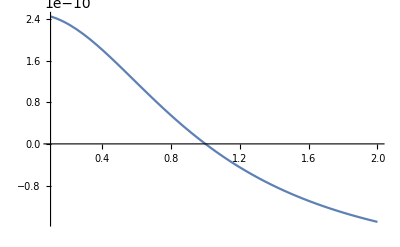

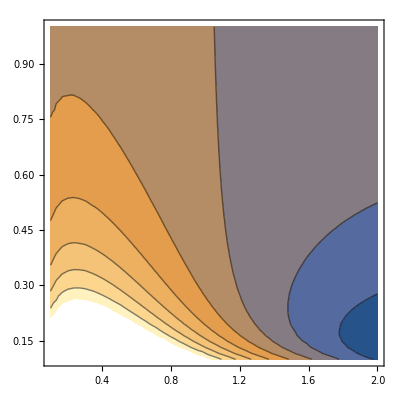

```mathematica
Plot[Subscript[COV, HP]/.subs,{dr,0.1,2}]
Plot[Subscript[COV, HP]/.subs2,{dr,0.1,2}]
Plot[Subscript[COV, HP]/.subs3,{dr,0.1,2}]
ContourPlot[Subscript[COV, HP]/.subs4,{dr,0.1,2},{M,0.1,1}]
```

```mathematica
Plot[Subscript[COV, HP]/.subs,{dr,0.1,2}]
```

```mathematica
Subscript[chp, num]=(Subscript[G, H] Subscript[G, P] (Subscript[B, H] (-Subscript[d, H]+(-Subscript[A, H]+Subscript[B, H]) Subscript[G, H]) Subscript[n, H]+Subscript[B, P] (Subscript[d, P]+(Subscript[A, P]+Subscript[B, P]) Subscript[G, P]) Subscript[n, P]))
```

G_H G_P (B_H (-d_H+(-A_H+B_H) G_H) n_H+B_P (d_P+(A_P+B_P) G_P) n_P)

```mathematica
Subscript[chp, den]=
(2 (Subscript[d, H]+Subscript[d, P]+(Subscript[A, H]-Subscript[B, H]) Subscript[G, H]+(Subscript[A, P]+Subscript[B, P]) Subscript[G, P]) (Subscript[d, H] (Subscript[d, P]+(Subscript[A, P]+Subscript[B, P]) Subscript[G, P])+Subscript[G, H] (-Subscript[B, H] (Subscript[d, P]+Subscript[A, P] Subscript[G, P])+Subscript[A, H] (Subscript[d, P]+(Subscript[A, P]+Subscript[B, P]) Subscript[G, P]))) Subscript[n, H] Subscript[n, P])
```

2 (d_H+d_P+(A_H-B_H) G_H+(A_P+B_P) G_P) (d_H (d_P+(A_P+B_P) G_P)+G_H (-B_H (d_P+A_P G_P)+A_H (d_P+(A_P+B_P) G_P))) n_H n_P

```mathematica
Simplify[Expand[Subscript[d, H] (Subscript[d, P]+(Subscript[A, P]+Subscript[B, P]) Subscript[G, P])+Subscript[G, H] (-Subscript[B, H] (Subscript[d, P]+Subscript[A, P] Subscript[G, P])+Subscript[A, H] (Subscript[d, P]+(Subscript[A, P]+Subscript[B, P]) Subscript[G, P]))]]
```

d_H (d_P+(A_P+B_P) G_P)+G_H (-B_H (d_P+A_P G_P)+A_H (d_P+(A_P+B_P) G_P))

```mathematica
Collect[Expand[Subscript[d, H] (Subscript[d, P]+(Subscript[A, P]+Subscript[B, P]) Subscript[G, P])+Subscript[G, H] (-Subscript[B, H] (Subscript[d, P]+Subscript[A, P] Subscript[G, P])+Subscript[A, H] (Subscript[d, P]+(Subscript[A, P]+Subscript[B, P]) Subscript[G, P]))]/.{Subscript[d, H] Subscript[d, P]->0},{Subscript[d, H],Subscript[d, P],Subscript[G, H] Subscript[G, P]}]
```

d_P (A_H G_H-B_H G_H)+(A_H A_P-A_P B_H+A_H B_P) G_H G_P+d_H (A_P G_P+B_P G_P)